# Conceptual Investigation on Waves in Physics

正如标题所示，我们的主题是 “波”！很多时候，我们学物理的人会问，“到底什么是波？”我也没有答案，我觉得可能也没有标准答案。因为，首先 “波”这个概念渗透在物理学的每个角落以至于我们有时对 “波”这个概念变得无所是从，比如机械波、电磁波、物质波、引力波等等，其次，很多时候 “波”是我们描述物理现象的一种概括，更深入地讲，是我们对这个客观物理世界认知的一种提炼，比如 “波”和 “粒子”。对于初学物理者来说并不能有很深刻具体可感的体会，但是 “波”这个概念是如此深刻和重要，所以在这里我们从最简单的情形入手让初学者能更深刻地对物理学中 “波”这一概念有跟简单而深刻的印象，以期在以后的学习和发展中能够再加以思考和运用，生发出自己的智慧！

## 1. Huygen’s Principle 在第一部分我们用惠更斯原理来模拟观察在波动现象中最为重要和显著的两个现象：衍射和干涉。通过对这两种现象的观察来认识“波”以及其最简单而深刻的特性：叠加性原理！关于波和波的干涉衍射，费曼物理学讲义第一卷中有很多值得阅读的讲解和诠释，强烈推荐！

### 1.1 Diffraction

我们知道我们观察到的衍射现象往往取决于入射波的波长和衍射孔的大小，或者更确切的说，波长和孔大小的比例，λ/d. 下面，我们用惠更斯原理来模拟衍射现象，并且调节各种参数比如λ/d来观察衍射现象。注意，在这里，为了节省内存和运行时间，我们省去时间相位项exp(-ⅈωt)，而仅仅只模拟出空间exp(ⅈkr)相位项，有兴趣的同学可以自己加上时间相位项并模拟出更生动的动画出来exp[ⅈ(kr-ωt)]。
       惠更斯原理的数学描述：w(r,t) = ∑_(m=1)^n exp[ⅈ(kr_m-ωt)]，其中，r_m= r - r_(0m)，r_(0m)为子波波源位置。

首先我们观察合波的实部因此用函数Re[]，画出xy平面上的波的传播图，和在假想接受观测屏y = L处的振幅图像。

```mathematica
Clear["Global`*"]
```

```mathematica
n=50;(*子波数目*)
d=1;(*衍射孔径*)
λ = 0.1;(*入射波长*)
L = 10;(*观察范围*)
(*在这里我们假设子波振幅不衰减，真实的情况可以是(exp(ⅈkr))/r 或者(exp(ⅈkr))/(√r)*)
u[p_,x_,y_,λ_]:=With[{k=(2π)/λ},Exp[ⅈ(k √((x-p)^2+y^2))]] (*子波*);
w[x_,y_,λ_]:=Sum[u[p,x,y,λ],{p,-d/2,d/2,d/n}]/n (*衍射合波*);
```

-Graphics-

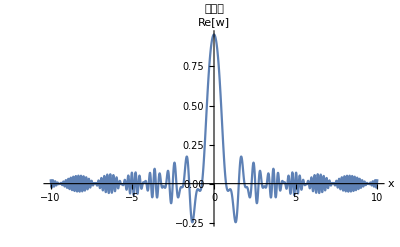

```mathematica
DensityPlot[Re[w[x,y,λ]],{x,-L,L},{y,-L,L},Mesh->None,PlotRange->All,PlotPoints->80,
PlotLegends->"Re[w]",PlotLabel->"波的传播"]
Plot[Re[w[x,L,λ]],{x,-L,L},PlotRange->All,AxesLabel->{"x","Re[w]"},PlotLabel->"接收屏"]
```

改变λ/d，使λ/d分别为0.5、1、1.5，画出图像，观察变化趋势！我们可以很明显的看到当波长相对于衍射孔径（λ/d）越大时衍射现象越明显！因为光波的波长很短以至于在我们人类的感知尺度下很难体现出其波动性，这也就是为什么光波（400nm~600nm）在我们的宏观世界中更体现出直线传播的特性，也就是粒子性！这也就是为什么几百年前物理学家最初从粒子的角度去解释光是什么了！而声波的波长（2cm~0.02cm）和我们人类的感知尺度很接近，因此更容易体现出其波动性的一面，因此物理学家很轻松成功地运用气体动力学就解释清楚了！而在下一节我们会着重谈一谈物理学家为何能用干涉现象感知光波的存在！

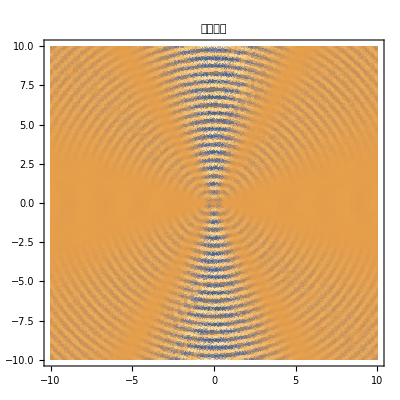
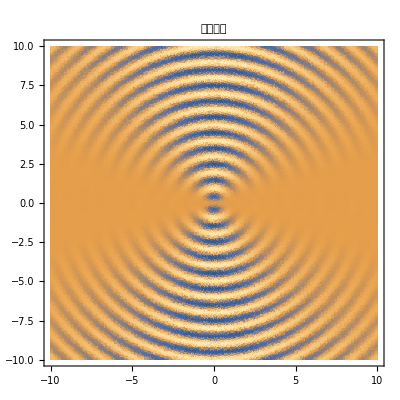
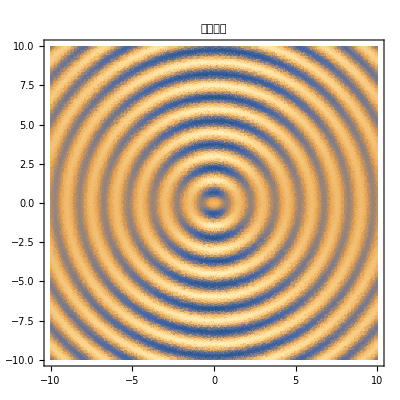

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[DensityPlot[Re[w[x,y,λ0]],{x,-L,L},{y,-L,L},Mesh->None,PlotRange->All,PlotPoints->50,PlotLegends->"Re[w]",PlotLabel->"波的传播"],{λ0,{0.5d,d,1.5d}}]
Table[Plot[Re[w[x,L,λ]],{x,-L,L},PlotRange->All,AxesLabel->{"x","Re[w]"},PlotLabel->"接收屏"],{λ0,{0.5d,d,1.5d}}]
```

### 1.2 Interference

我们将干涉现象简单的描述为两个不同位置的子波的叠加，即w(r,t) = exp[ⅈ(kr_1-ωt)] + exp[ⅈ(kr_2-ωt)]. 通过调节各种参数如波长与波源间距之比λ/d、观察范围视野L，我们来对波的干涉有一个初步感性的认知，并且我们试图用这一简单的物理现象去展示“波”的一个非常重要的属性：相位！

我们观察两个子波源的合波的强度，因此用函数Abs[]，画出xy平面上的的传播图，和在假想接受观测屏y = L处的振幅图像。

```mathematica
Clear["Global`*"]
```

```mathematica
n=2;(*子波数目*)
d=1;(*波源间距*)
λ =0.02;(*入射波长*)
L = 100;(*观察范围*)
u[p_,x_,y_,λ_]:=With[{k=(2π)/λ},Exp[ⅈ(k √((x-p)^2+y^2))]] (*子波*);
w[x_,y_,λ_]:=Sum[u[p,x,y,λ],{p,-d/2,d/2,d/n}]/n (*衍射合波*);
```

-Graphics-

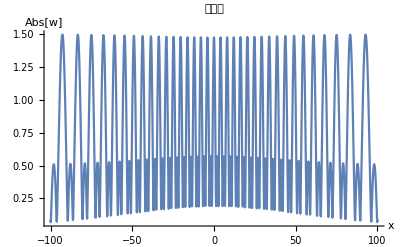

```mathematica
DensityPlot[Abs[w[x,y,λ]],{x,-L,L},{y,-L,L},Mesh->None,PlotRange->All,PlotPoints->80,
PlotLegends->"Abs[w]",PlotLabel->"波的传播"]
Plot[Abs[w[x,L,λ]],{x,-L,L},PlotRange->All,AxesLabel->{"x","Abs[w]"},PlotLabel->"接收屏"]
```

改变λ/d，使λ/d分别为0.1、0.5、1，画出图像，观察变化趋势！当λ/d越来越大时，可以观测到的条纹数变得越来越少，或者说角度条纹与条纹之间的角度间距Δθ越来越大，越来越容易看出干涉条纹！另外一方面，如果我们的仪器精密度或者我们物理学家的感知月灵敏的话，我们越能够通过干涉来研究“波”的特性！因为λ/d越来越大时条纹的角度间距Δθ越来越大，而如果我们把观测屏幕离光源很远，那么条纹之间的空间间距ΔL=LΔθ就能越大，这就是为什么Thomas Young能够通过双缝干涉观察到波长在500nm量级的光波的干涉现象了！
       接着，我们来谈一谈相位这个概念！最简单的讲，相位就是我们高中数学中正弦函数自变量x后面多加上的一个常数φ：sin(x+φ)。大学我们学到机械波或者简谐振动中的相位，我们说相位就是描述某个动作或者振动的先后步调。那么，我们还会在光学或者电磁场的波动和量子物理中见到相位这个概念，你是否会问，一个物理概念比如“波”或者我们这里说的“相位”（波的一个重要属性）如此深刻地渗透到整个学科的各个角落到底有着什么深刻内涵？这里，我只能抛砖引玉似地通过一些物理现象去提出自己的思考。首先，我最开始注意到的就是，相位φ是一个没有量纲的量（如果有的话，我也想可以是2π，即一个周期的度量），也就是说相位可以出现在任何一个时空尺度的物理世界，比如宏观世界、量子世界甚至宇观世界，只要有波动存在的地方就要有相位的出现，所以这也试图说明了相位为什么会出现在物理学的很多地方！其次，我们回想与相位相关的物理现象一定会出现相位差，也就是说，我们更关注的是两束”波”的相对相位，比如光的干涉、电子物质波的干涉等。然后，我们从数学上看，任何波总是可以写成exp[ⅈ(kr-ωt)]形式的叠加，ω为时间角频率，k为波数或者空间角频率，如果我们把他们合起来成为时空角频率记作K=(k_x, k_y, k_z, ω)，然后我们就可以明白当K在不同的量级，也就是相位变化快慢在不同量级时，相对相位变化也就在不同量级。所以，我的初步结论是，物理量的相对变化快慢通过时空的流逝以“波”的相位的概念在物理学中体现出来，并且在整个物理学中展现出丰富多彩变幻无穷的物理现象和其后引人深思而深刻的物理内涵！

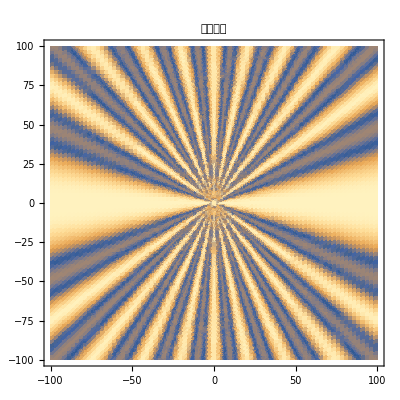
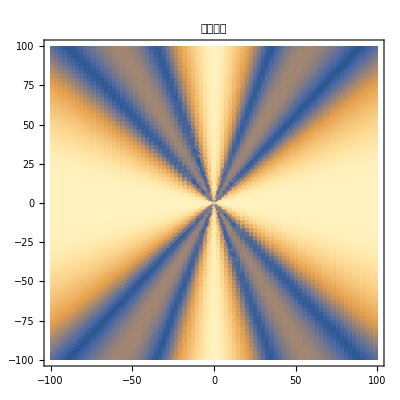
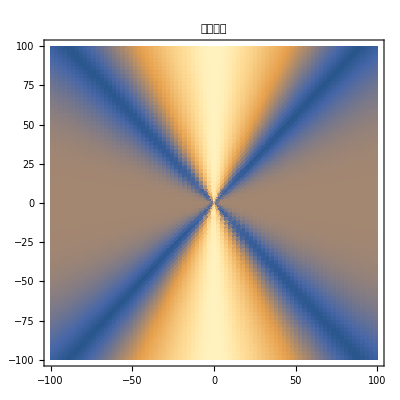

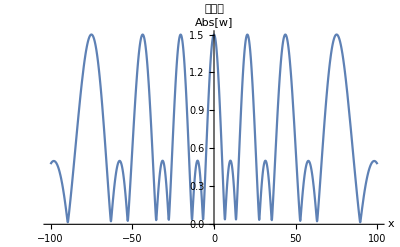
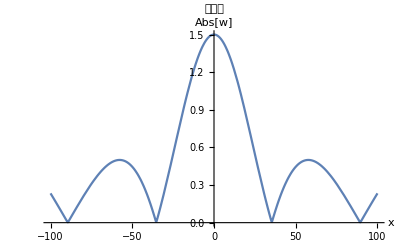
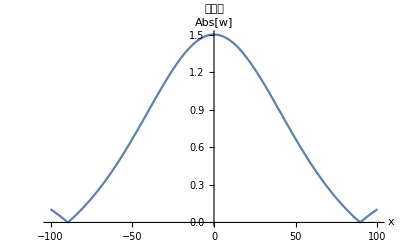

```mathematica
Table[DensityPlot[Abs[w[x,y,λ0]],{x,-L,L},{y,-L,L},Mesh->None,PlotRange->All,PlotPoints->80,PlotLegends->"Abs[w]",PlotLabel->"波的传播"],{λ0,{0.1 d,0.5d,d}}]
Table[Plot[Abs[w[x,L,λ0]],{x,-L,L},PlotRange->All,AxesLabel->{"x","Abs[w]"},PlotLabel->"接收屏"],{λ0,{0.1 d,0.5d,d}}]
```

## 2. Wave Package 在第二部分，我们将通过波的叠加的一些简单示例来试图探讨一个深刻而又深远的物理思想：叠加性原理！我们前前后后或明或隐地都在运用这一点，但在这里我们只是强调叠加性原理的重要性而并不打算对此展开深入探讨。我们先从简单两束频率相差很小的波叠加产生拍频的现象开始，接着模拟在一个频率临域的几束波的线性叠加，然后推广到一个频率临域内无限束波的叠加时合成Dirac-delta函数的情况。在这里我们考察波的一种简单而特殊的叠加，但是这里蕴含的深刻物理数学思想将是我们学习物理的同学在以后的学习和发展生涯中不断面临和碰到的问题和解决问题的途径之一！更详细的数学推到参见文件最后。

### 2.1 Superposition of two waves

下面是简单的两列波叠加产生拍频的演示动画。

```mathematica
Manipulate[
Animate[Plot[Sin[ω t-k r]+Sin[(ω+2Pi 0.005) t-(k+2Pi 0.005) r],{r,0,1000},PlotRange->2],{t,0,Infinity},AnimationRunning->False],{{ω,2Pi,"ω"},0,2Pi 50},{{k,(2Pi)/2,"k"},0,(2Pi)/1}]
```

### 2.2 Superposition of several waves

我们考虑在一个很小的频率临域里很多很多列波的叠加。当叠加数越多时，我们很明显地发现波包变得越来越窄，波包之间的间距越来越大，如果我们有无数列波叠加，那么最后只会在原点有一个非常尖锐的波包或者峰！在下一小节我们将深入地从数学上探讨这一物理图像！

```mathematica
Manipulate[Animate[Plot[Sum[Sin[(ω+δω) t-(k+δω) r],{δω,0,2Pi 0.01,(2Pi 0.01)/n}]/n,{r,0,1000},PlotRange->1],{t,0,Infinity},AnimationRunning->False],{{ω,2Pi,"ω"},2Pi,2Pi 20},{{k,(2Pi)/2,"k"},0,2Pi},{{n,5,"number of waves"},1,50,1}]
```

```mathematica
Manipulate[Plot[Sin[x]/(n Sin[x/n]),{x,-200,200},PlotRange->3],{n,1,50}]
```

### 2.3 Superposition of waves in the whole “Frequency Space”: Dirac-delta Function δ(x)

在这一小节，我们只将简单地展示傅立叶积分在频率全空间积分的结果，并通过此来引出其后给我们的物理启示。
       在一维傅里叶变换的情形下，我们有
                                                            时域t： Piecewise[{{f̃(ω)=1/(√(2π))∫_(-∞)^(+∞) f(t)exp[-ⅈωt]ⅆt
f(t)=1/(√(2π))∫_(-∞)^(+∞) f̃(ω)exp[ⅈωt]ⅆω, }}],
                                                            空间x：Piecewise[{{f̃(k)=1/(√(2π))∫_(-∞)^(+∞) f(x)exp[-ⅈkx]ⅆt
f(x)=1/(√(2π))∫_(-∞)^(+∞) f̃(k)exp[ⅈkx]ⅆω, }}].
       那么，如果我们考虑把全频域空间的波都叠加起来，即f̃(ω) = 1，f(t) = 1/(√(2π))∫_(-∞)^(+∞) exp[ⅈωt]ⅆω= √(2π)δ(t)。同样的，如果f̃(k) = 1，那么f(x) = 1/(√(2π))∫_(-∞)^(+∞) exp[ⅈkx]ⅆk = √(2π)δ(x)，即δ(x)=1/(2π)∫_(-∞)^(+∞) exp[ⅈkx]ⅆk 。如果Dirac-delta函数有一个偏置x_0，那么δ(x-x_0)=1/(2π)∫_(-∞)^(+∞) exp[ⅈk(x-x_0)]ⅆk。我们对此的物理图像是，全频域空间的波叠加起来将在原点处存留下一个非常尖锐的峰，或者更具物理图像的解释是，某一位置的一个点粒子可以是某全频率空间所有波的叠加！反过来我们也有δ(k-k_0)=1/(2π)∫_(-∞)^(+∞) exp[ⅈ(k-k_0)x]ⅆx，那么，某一频率的波可以是某全空间所有粒子的叠加！
       在三维空间和四维时空中的傅里叶变换分别为，
                                                           三维空间： Piecewise[{{f̃(k)=(1/(√(2π)))^3∫_(-∞)^(+∞) f(x)exp[-ⅈk·x]ⅆ^3 x
f(x)=(1/(√(2π)))^3∫_(-∞)^(+∞) f̃(k)exp[ⅈk·x]ⅆ^3 k
x=(x,y,z,t), ⅆ^3 x=ⅆxⅆyⅆz,
k=(k_x,k_y,k_z) , ⅆ^3 k=ⅆ k_xⅆ k_yⅆ k_z., }}]
                                                           四维时空： Piecewise[{{f̃(K)=(1/(√(2π)))^4∫_(-∞)^(+∞) f(X)exp[-ⅈ(kr-ωt)]ⅆ^4 X
f(X)=(1/(√(2π)))^4∫_(-∞)^(+∞) f̃(K)exp[ⅈ(kr-ωt)]ⅆ^4 K
X=(x,y,z,t), ⅆ^4 X=ⅆxⅆyⅆzⅆt,
K=(k_x,k_y,k_z,ω) , ⅆ^4 K=ⅆ k_xⅆ k_yⅆ k_zⅆω., }}]
       所以我们可以推广到四维时空和四维频率空间中粒子与波之间的变换关系，通过对Dirac-delta函数的傅里叶变换的探讨，我们可以这么说，波和粒子只是我们观察这个世界对偶的两种方式或者表象，而通过前几节的探讨我们也可以说，在不同的情形下我们更倾向性地看到的是某一个表象，而这两者又是相互联系，不能说哪一个是更本质的！

## 3. From Hugen’s Principle to Fourier Decomposition

此部分为进阶部分，作为对有兴趣的同学的一个拓展延伸。
       惠更斯原理从数学上来说是球面波分解，第二部分的主要内容是属于傅里叶级数分解或者平面波分解的内容，两者在现代物理分析的方法中是两大主导！因此，有兴趣的同学可以查阅相关书籍或者资料，用mathematica来展示两者间的深刻联系与区别！
       在此我们仅从数学结论上给出两者之间的关系。设有一平面波为exp[ⅈk·r] = exp[ⅈkrcosθ]，则
                                                            exp[ⅈkrcosθ]=∑_(l=0)^∞ (2l+1)ⅈ^l j_l(kr)P_l(cosθ).
其中，P_l(cosθ)为勒让德多项式，j_l(kr)为球贝塞尔函数（r→∞,j_l(kr)→(cos(kr-(l+1)/2 π))/kr~1/kr(exp[ⅈkr]+exp[-ⅈkr])/2）。

```mathematica
Clear["Global`*"]
```

```mathematica
θ=π/6;(*平面波倾角*)
k=(2π)/1;(*平面波波数*)
L=5;(*观察范围*)
l=20;(*球面波的叠加数*)
wplain[x_,y_]:=Re[Exp[ⅈ k(x Sin[θ]+y Cos[θ])]];
wspheri[x_,y_]:=Re[Sum[(2n+1)ⅈ^n SphericalBesselJ[n,k √(x^2+y^2)] LegendreP[n,-Cos[θ]],{n,0,l}]];
```

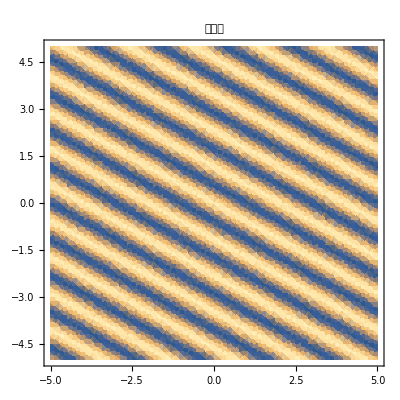

-Graphics-

```mathematica
DensityPlot[wplain[x,y],{x,-L,L},{y,-L,L},Mesh->None,PlotRange->All,PlotPoints->20,PlotLabel->"平面波"]
DensityPlot[wspheri[x,y],{x,-L,L},{y,-L,L},Mesh->None,PlotRange->All,PlotPoints->30,PlotLabel->"球面波的叠加"]
```

# Appendix: wave superposition

Discrete Situation : 
Finite number of waves in the vicinity of a point in the frequency domain forms a quasi Sinc function wave
 Continuous Situation:
With fourier transformation applied to a frequency inverval, the integrated waves appear to  be a Sinc-funtion-like shape.
For the first situation, we have,
ϕ(r,t)=(1/n∑)_(k=0)^(n-1)ⅇ^(ⅈ((ω+k δ)t+(k+β k δ)r)),
where β =ⅆk/ⅆω,δ=δω/n.
Take the real part of ϕ(r,t), we have,
ϕ(r,t)=(sin(δω/2(t-βr)))/(n sin(δω/(2n)(t-βr)))cos(ω t -k r +δω/(2n)(t-βr)).
When n goes infinite, we obtain the same result as the continuous situation,
ϕ(r,t)=(sin(δω/2(t-βr)))/(δω/2(t-βr))cos(ω t -k r ).
For the second situation, by directly integrating, we have,
ϕ(r,t)=∫_0^δω 1/δω ⅇ^(ⅈ((ω+δ)t+(k+β δ)r))ⅆδ
                 = ⅇ^(ⅈ(ω t+k r))(ⅇ^(ⅈ δω(t+β r))-1)/(δω(t-β r))
                 =ⅇ^(ⅈ((ω+δω/2)t+(k+β δω/2)r))sinc(δω/2(t-β r)).

## 1. Superposition of two waves

```mathematica
Manipulate[
Animate[Plot[Sin[ω t-k r]+Sin[(ω+2Pi 0.005) t-(k+2Pi 0.005) r],{r,0,1000},PlotRange->2],{t,0,Infinity},AnimationRunning->False],{{ω,2Pi,"ω"},0,2Pi 50},{{k,(2Pi)/2,"k"},0,(2Pi)/1}]
```

## 2. Superposition of several waves

```mathematica
Directly sum up several waves
```

```mathematica
Manipulate[Animate[Plot[Sum[Sin[(ω+δω) t-(k+δω) r],{δω,0,2Pi 0.01,(2Pi 0.01)/n}]/n,{r,0,1000},PlotRange->1],{t,0,Infinity},AnimationRunning->False],{{ω,2Pi,"ω"},2Pi,2Pi 20},{{k,(2Pi)/2,"k"},0,2Pi},{{n,5,"number of waves"},1,50,1}]
```

```mathematica
Illustration of the package shape
```

```mathematica
Manipulate[Plot[Sin[x]/(n Sin[x/n]),{x,-200,200},PlotRange->3],{n,1,50}]
```

```mathematica
Animate[Plot[Sin[(2Pi 0.01)/2(t- r)]/(5 Sin[(2Pi 0.01)/10(t-r)])Cos[2Pi t-Pi r],{r,0,1000},PlotRange->1],{t,0,Infinity},AnimationRunning->False]
```

```mathematica
Use the formula obtained in the preceding section to test its validity
```

```mathematica
Animate[Plot[Sin[(2Pi 0.01)/2(t- r)]/(5 Sin[(2Pi 0.01)/10(t-r)])Cos[2Pi t-Pi r],{r,0,1000},PlotRange->1],{t,0,Infinity},AnimationRunning->False]
```

```mathematica
Illustration of the package shape
```

```mathematica
Manipulate[Plot[Sin[x]/(n Sin[x/n]),{x,-200,200},PlotRange->3],{n,1,50}]
```

作者：刘开锴